The goal of this notebook is simply to collect and organize all of the work that Vijay has already done in the various other Mathematica notebooks. This will hopefully be useful as a check by a second pair of eyes, and as a confirmation that all of our numbers and plots are up-to-date and final with our current understanding of physics.

# White dwarf parameters

Here we define various physical parameters of the white dwarf, which are used frequently in this notebook. They are defined as functions of white dwarf mass or density, where appropriate.

Let’s say that the following are the minimum and maximum white dwarf masses of interest, which are ultimately what we care about for plotting and discussion.

```mathematica
Mmin=0.85;
Mmax=1.37;
```

## White dwarf mass and radius data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/priggins/Dropbox/Berkeley-current/Research/WhiteDwarfParticleDetector/Qballs

Density-mass relation and number densities

## Density-mass relation

Density-mass relation and its inverse, with density in g/cm^3 and mass in M_☉.

```mathematica
WDLogDensityMassData=Import["WD.csv"];
WDDensityMassData={10^(#[[1]]),#[[2]]}&/@WDLogDensityMassData;
WDDensityMassCGS=Interpolation[WDDensityMassData]
WDMassDensityCGS=Interpolation[Reverse/@WDDensityMassData]
```

10
InterpolatingFunction[{{11437.4, 5.43438 10  }}, <>]

InterpolatingFunction[{{0.0405266, 1.40072}}, <>]

Similarly, with densities in units of MeV^4,

```mathematica
Quantity[1.,"Grams"/("Centimeters")^3]/Quantity[1.,("Megaelectronvolts")^4/(("SpeedOfLight")^5("ReducedPlanckConstant")^3)]//UnitConvert
```

4.31013×10^-6

```mathematica
WDDensityMassDataInMeV={Quantity[#[[1]],"Grams"/("Centimeters")^3]/Quantity[1.,("Megaelectronvolts")^4/(("SpeedOfLight")^5("ReducedPlanckConstant")^3)],#[[2]]}&/@WDDensityMassData;
WDDensityMassMeV=Interpolation[WDDensityMassDataInMeV]
WDMassDensityMeV=Interpolation[Reverse/@WDDensityMassDataInMeV]
```

InterpolatingFunction[{{0.0492968, 234229.}}, <>]

InterpolatingFunction[{{0.0405266, 1.40072}}, <>]

Some example densities as functions of mass:

```mathematica
{WDMassDensityCGS[0.85],WDMassDensityCGS[1.25],WDMassDensityCGS[1.37]}
{WDMassDensityMeV[0.85],WDMassDensityMeV[1.25],WDMassDensityMeV[1.37]}
```

{1.44744×10^7,2.88397×10^8,3.22949×10^9}

{62.3864,1243.03,13919.5}

## Ion and electron number densities

We know compute the ion and electron number densities as a function of white dwarf mass. Note that our ions are carbon with mass = 12*m_p and charge Z=6.

### Ion number density

In units of cm^-3,

```mathematica
nIonCGS[M_]:=WDMassDensityCGS[M] Quantity[1.,"Grams"]/Quantity[12,"ProtonMass"];
Table[nIonCGS[M],{M,{0.85,1.25,1.37}}]
```

{7.21141×10^29,1.43685×10^31,1.609×10^32}

And in units of MeV^3,

```mathematica
nIonMeV[M_]:=WDMassDensityMeV[M] Quantity[1.,"Megaelectronvolts"]/Quantity[12,"Gigaelectronvolts"];
Table[nIonMeV[M],{M,{0.85,1.25,1.37}}]
```

{0.00519886,0.103586,1.15996}

### Electron number density

In units of cm^-3,

```mathematica
nElectronCGS[M_]:=nIonCGS[M]*Z/.{Z->6};
Table[nElectronCGS[M],{M,{0.85,1.25,1.37}}]
```

{4.32685×10^30,8.62111×10^31,9.65397×10^32}

And in units of MeV^3,

```mathematica
nElectronMeV[M_]:=nIonMeV[M]*Z/.{Z->6};
Table[nElectronMeV[M],{M,{0.85,1.25,1.37}}]
```

{0.0311932,0.621515,6.95976}

Mass-radius relation and escape velocity

## Mass-radius relation

Mass-radius relation and its inverse, with mass in M_☉ and radius in km. (The radius is originally in R_☉ in the data file, which must be converted.).

```mathematica
WDMassRadiusData=Import["WDradius.csv"];
WDMassRadiusDataConvertedToKilometers={1,Quantity[1.,"SolarRadius"]/Quantity[1.,"Kilometers"]}*#&/@WDMassRadiusData;
WDMassRadius=Interpolation[WDMassRadiusDataConvertedToKilometers]
WDRadiusMass=Interpolation[Reverse/@WDMassRadiusDataConvertedToKilometers]
```

InterpolatingFunction[{{0.0407984, 1.42331}}, <>]

InterpolatingFunction[{{328.863, 19770.4}}, <>]

## Escape velocity

Here is the escape velocity as a fraction of c, again as a function of white dwarf mass.

```mathematica
vesc[M_]:=1/c √((2G Mwd)/R)/.
{G->Quantity[1.,"GravitationalConstant"],
R->Quantity[WDMassRadius[M],"Kilometers"],
Mwd->Quantity[M,"SolarMass"],
c->Quantity[1.,"SpeedOfLight"]}//UnitConvert;
Table[vesc[M],{M,{0.85,1.25,1.37}}]
```

{0.0198225,0.0333143,0.0463183}

## Plasma and Lattice parameters

Thomas-Fermi length:

Plasma frequency:

Debye energy:

# Trigger size and boom energies

Here we calculate the trigger size and minimum energy deposits necessary for explosion as functions of white dwarf density and mass.

## Trigger size

Here is the trigger size in cm^-3 as a function of white dwarf density and mass:

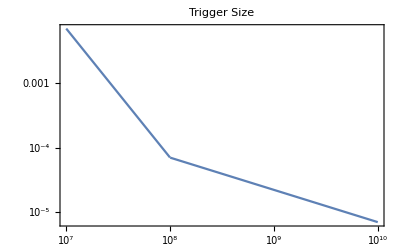

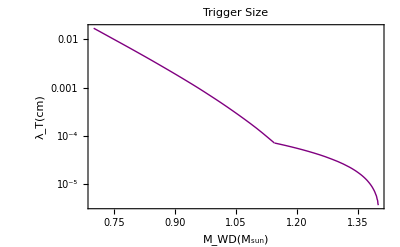

```mathematica
triggerDensityCGS[ρCGS_]:=
Return@If[ρCGS>10^8,10^-5*(ρCGS/(5*10^9))^(-1/2),1/(10000 √2)*(ρCGS/10^8)^-2];
triggerMass[M_]:=Module[{ρ},
ρ=WDMassDensityCGS[M];
Return@If[ρ>10^8,10^-5*(ρ/(5*10^9))^(-1/2),1/(10000 √2)*(ρ/10^8)^-2]
];

LogLogPlot[{triggerDensityCGS[ρ]},{ρ,10^10,10^7},PlotLabel->"Trigger Size",Frame->True]
LogPlot[triggerMass[M],{M,0.7,1.4},PlotLabel->"Trigger Size",Frame->True,PlotStyle->{Thick,Purple},FrameLabel->{"M_WD(M_sun)","λ_T(cm)"},FrameStyle->Black]
```

```mathematica
Table[Quantity[triggerMass[M],"Centimeters"],{M,{0.85,1.25,1.37}}]//ScientificForm
```

{3.3751×10^-3 cm,4.1638×10^-5 cm,1.24428×10^-5 cm}

## E_boom

The minimum energy deposit necessary to explode the white dwarf is given here in GeV as a function of white dwarf mass:

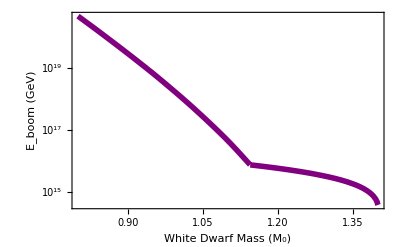

```mathematica
eboom[M_]:=Log10[(nIonCGS[M]*(4π)/3(λT)^3 Tmin)/Quantity[1.,"Gigaelectronvolts"]]/.{λT->triggerMass[M],Tmin->Quantity[1.,"Megaelectronvolts"]};

eboomreverse[mdm_]:=Interpolation[Table[{eboom[M],M},{M,0.4,1.40,0.01}],InterpolationOrder->1][mdm]
XLabelEboom = {{0.2, "0.2"},{0.3, "0.3"},{0.4, "0.4"},{0.5, "0.5"}, {0.6, "0.6"},{0.7, "0.7"},  {0.8, "0.8"},{0.9, "0.9"}, {1.0, "1.0"},{1.1, "1.1"}, {1.2, "1.2"},{1.3, "1.3"}, {1.4, "1.4"}}; 
YLabelEboom = {{15, "10^15"}, {16, "10^16"},{17, "10^17"}, {18, "10^18"}, {19, "10^19"},  {20, "10^20"},{21, "10^21"},{22, "10^22"},{23, "10^23"}}; 
YEboom = {{15, ""}, {16, ""},{17, ""}, {18, ""}, {19, ""},  {20,""},{21, ""},{22, ""},{23, ""}};
Eboom=Plot[eboom[M],{M,0.8,1.40},Frame->True,FrameTicks-> {{YLabelEboom,YEboom},{Automatic,None}},FrameLabel->{"White Dwarf Mass (M_0)","E_boom (GeV)"},FrameStyle->Black,PlotStyle-> {Purple,Thickness[0.01]}, LabelStyle-> Directive[Bold]]
```

```mathematica
Table[Quantity[10^eboom[M],"Gigaelectronvolts"],{M,{0.85,1.25,1.37}}]
```

{1.16136×10^20 GeV,4.34479×10^15 GeV,1.29837×10^15 GeV}

# Collision processes and stopping powers

Here we gather and compute the stopping powers for all the various collision processes (Coulomb, hadronic shower, etc.) that energetic particles in a white dwarf might undergo.

## Pions and nucleons

Hadronic shower

Low-energy elastic scatters

Once pions and nucleons have sufficiently low-energy (below 10 MeV), they can hadronically scatter of ions either elastically (transferring a fraction of their kinetic energy and then bouncing off).

At this point, the particles are non-relativistic. Conservation of momentum and energy demands

```mathematica
Solve[{1/2 m vi^2==1/2 m vf^2+1/2 M v^2,m vi==m vf Cos[θ]+M v Cos[ψ],0==m vf Sin[θ]-M v Sin[ψ]},vf,{ψ,v}]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{vf→(2 m vi Cos[θ]-√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))},{vf→(2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M))}}

The second solution is the physical one, so the incident particle has final energy

```mathematica
Efin=1/2 m((2 m vi Cos[θ]+√2 √(vi^2 (-m^2+2 M^2+m^2 Cos[2 θ])))/(2 (m+M)))^2/.vi->Sqrt[2 ϵ/m];
```

assuming the incident particle had initial energy ϵ. The incident particle retains a fraction of its initial energy given by

```mathematica
Eretained=FullSimplify[Efin/ϵ,Assumptions->{ϵ>0,M>0,m>0}];
```

The average fraction ζ retained, considering all possible angles of scatter and assuming the particle scatters isotopically, is

```mathematica
ζel=1/(2Pi)Integrate[Eretained,{θ,0,2Pi},Assumptions->{ϵ>0,M>0,m>0}]//FullSimplify
```

M^2/(m+M)^2

A proper calculation (lab frame angle not exactly isotropic, unlike CM angle) yields ζ= (M^2+m^2)/(m+M)^2~M^2/(m+M)^2for heavy nuclei, so our estimate here is good.

Since a light incident particle retains most of its energy after collision with a heavy incident particle, it will perform a random walk with several collisions before it has transferred O(1) of its initial energy. The number of steps nn is

```mathematica
Solve[ζel^nn==0.2/.{M->12000,m->100},nn]//Quiet(* pion *)
```

{{nn→96.9681}}

```mathematica
Solve[ζel^nn==0.2/.{M->12000,m->1000},nn]//Quiet(* neutron/proton, ignoring electromagnetic scatters *)
```

{{nn→10.0536}}

Since this is a random walk, the particle will travel a distance √nn λ, where λ=(n_ion σ)^-1 is the mean free path. The stopping powers are therefore

```mathematica
dedxElasticMeson=Piecewise[{{ϵ/(√nn(nion*σElasticMeson)^-1)/.nn->100,ϵ≤10},{0,ϵ>10}}];
dedxElasticNucleon=Piecewise[{{ϵ/(√nn(nion*σElasticNucleon)^-1)/.nn->10,ϵ≤10},{0,ϵ>10}}];
```

Note this is different from Vijay’s notebook, where the square root was not included. (numerically probably not a significant difference)

Low-energy inelastic scatters

In principle, a neutron or pion could also be inelastically absorbed by the ion. The neutron capture cross section for carbon is famously low, which is why it is useful as a moderator for nuclear reactors. There is a 3 order of magnitude difference between the scattering and capture cross-sections for neutrons in carbon.

As for pions ......

Nonelastic scatters

When the energy is too high, the particles will non-elastically scatter instead, disintegrating the ions they hit:

```mathematica
dedxNonelastic=Piecewise[{{ϵ (nion σ),ϵ>10},{0,ϵ≤10}}];
```

Phonon production

Most likely not important, will ignore for now

## Electrons and photons

Coulomb collisions

## Phonon production

Compton and inverse compton scattering

Bremsstrahlung and pair production

Photonuclear and electronuclear interactions

# Generic constraints

Here we compute and plot constraints for transits, collisions, and decays for generic heavy dark matter candidates.

# Q-balls constraints

Here we compute and plot constraints for Q-balls specifically.